# Thermoelectrics vs Effective Mass (P+IP Multiband) w/ deformation-potential and polar-optical scattering w/ Brooks-Herring theory for ionized-impurity scattering

### Units, Conversions, and Constants

```mathematica
Clear[en,k,m,mu,kx,ky,kz];Needs["PlotLegends`"];Needs["FunctionApproximations`"]

h2ev=27.211;ev2j=1.602*10^-19;q=1.602*10^-19;mass=9.11*10^-31;bohr2m=5.29*10^-11;
au2sec=2.4188*10^-17;au2cond=(q/au2sec)^2/bohr2m^3*au2sec^3/mass;

gap=0/h2ev;kB=8.6173303*10^-5/h2ev;T=500;
ω=kB*T/2;kappalat=0.5/(h2ev*ev2j/bohr2m/au2sec);
```

### Band structure - Parabola+InvParabola

```mathematica
(* Lattice and BZ *)
bz=(1/15.)*2π/2;volume=bz^-3*(2π/2)^3/8;
fix=1;

(* Effective Masses *)
mxc={0.05,0.15,0.5,1.5,5,15,50,150,500,  0.05,0.05,0.05,0.05,0.05, 0.05,0.05,0.05,0.05,0.05 };
myc={0.05,0.15,0.5,1.5,5,15,50,150,500,  0.05,0.05,0.05,0.05,0.05, 0.05,0.5,5,50,500};
mzc={0.05,0.15,0.5,1.5,5,15,50,150,500,  0.05,0.5,5,50,500, 0.05,0.5,5,50,500};
Nm=Length[mxc];
mdosc=(mxc*myc*mzc)^(1/3);mdosv=mdosc;

(* Fermi Level *)
Ef=Range[-0.2,0.2,0.01]/h2ev;
Nef=Length[Ef];
ef0=Position[Ef,0.]⟦1,1⟧;

Evpara=(-(kx^2/(2mx)+ky^2/(2my)+kz^2/(2mz))-gap/2)/.{mx->mxv,my->myv,mz->mzv};Ecpara=((kx^2/(2mx)+ky^2/(2my)+kz^2/(2mz))+gap/2)/.{mx->mxc,my->myc,mz->mzc};

inflect=0.5*bz;
slopex=D[Ecpara,kx]/.{kx->inflect,ky->0,kz->0};
slopey=D[Ecpara,ky]/.{ky->inflect,kx->0,kz->0};
slopez=D[Ecpara,kz]/.{kz->inflect,ky->0,kx->0};
mxcnew={};mycnew={};mzcnew={};
For[i=1,i≤Length[slopex],i++,
AppendTo[mxcnew,Solve[(bz-inflect)==x*slopex⟦i⟧]⟦All,1,2⟧⟦1⟧];
AppendTo[mycnew,Solve[(bz-inflect)==y*slopey⟦i⟧]⟦All,1,2⟧⟦1⟧];AppendTo[mzcnew,Solve[(bz-inflect)==z*slopez⟦i⟧]⟦All,1,2⟧⟦1⟧];
]

(*edge[kx_,ky_,kz_]:=Module[{x,y,z,scale},
scale=bz/(Max[Abs[kx],Abs[ky],Abs[kz]]+10^-15);
x=kx*scale;y=ky*scale;z=kz*scale;
Return[{{x,y,z},Norm[{x,y,z}]}]
]*)

width[kx_,ky_,kz_]:=Module[{width},
If [inflect≥0.5*bz,
(*bzx=edge[kx,ky,kz]⟦1,1⟧;bzy=edge[kx,ky,kz]⟦1,2⟧;bzz=edge[kx,ky,kz]⟦1,3⟧;*)
width=gap/2+((Min[Norm[kx],inflect])^2/(2mxc)+(inflect^2-(bz-Max[Norm[kx],inflect])^2)/(2mxcnew))+((Min[Norm[ky],inflect])^2/(2myc)+(inflect^2-(bz-Max[Norm[ky],inflect])^2)/(2mycnew))+((Min[Norm[kz],inflect])^2/(2mzc)+(inflect^2-(bz-Max[Norm[kz],inflect])^2)/(2mzcnew))-(Norm[(inflect^2-(bz-inflect)^2)]/2(1/mxcnew+1/mycnew+1/mzcnew)),
width=gap/2+((Min[Norm[kx],inflect])^2/(2mxc)+(inflect^2-(bz-Max[Norm[kx],inflect])^2)/(2mxcnew))+((Min[Norm[ky],inflect])^2/(2myc)+(inflect^2-(bz-Max[Norm[ky],inflect])^2)/(2mycnew))+((Min[Norm[kz],inflect])^2/(2mzc)+(inflect^2-(bz-Max[Norm[kz],inflect])^2)/(2mzcnew))+(Norm[(inflect^2-(bz-inflect)^2)]/2(1/mxcnew+1/mycnew+1/mzcnew))
];
Return[width]
]
Ec=width[kx,ky,kz];Ev=-width[kx,ky,kz];

(*r=Sqrt[kx^2/(2mxcnew)+ky^2/(2mycnew)+kz^2/(2mzcnew)];*)
(*Ecnew=(width-(bz*Sqrt[1/(2 minmass)]-r)^2)+gap/2;*)
(*Ecnew=(width[kx,ky,kz]-((edge[kx,ky,kz]⟦2⟧)/Sqrt[kx^2+ky^2+kz^2+10^-20]-1)^2 r^2)+gap/2;*)
(*Ecnew=(width[kx,ky,kz]-((edge[kx,ky,kz]⟦2⟧)/(Norm[{kx,ky,kz}]+10^-20)-1)^2 r^2)+gap/2;*)
(*Evnew=(-width+((edge[kx,ky,kz]⟦2⟧)/Sqrt[kx^2+ky^2+kz^2]*r-r)^2)-gap/2;*)
(*Chop[D[Ecnew,kz]/.{kx->0,ky->0,kz->bz}];
Chop[D[Ecnew,kx]/.{kx->bz,ky->0,kz->0}];*)

Eint=3/4*kB*T*Log[mdosv⟦1⟧/mdosc⟦1⟧];
Ev=Ev-Eint;Ec=Ec-Eint;
Vc=Transpose[{D[Ec,kx],D[Ec,ky],D[Ec,kz]}]/.{Norm'[kx]->D[Sqrt[kx^2],kx],Norm'[ky]->D[Sqrt[ky^2],ky],Norm'[kz]->D[Sqrt[kz^2],kz]};
Vv=Transpose[{D[Ev,kx],D[Ev,ky],D[Ev,kz]}](*/.{Norm'[kx]->Norm[kx],Norm'[ky]->Norm[ky],Norm'[kz]->Norm[kz]}*);

id=1;
Plot3D[{Ec⟦1⟧/.kz->0,Ec⟦id+1⟧/.kz->0},{kx,-bz,bz},{ky,-bz,bz},BoxRatios->{1,1,2},BoxStyle->Directive[Black,Thick,25],AxesLabel->{"k_x","k_y",Rotate["Energy (Ha)",π/2]},LabelStyle->{15},PlotRange->{Automatic,Automatic,{0,0.45}},PlotStyle->{Directive[Cyan],Directive[Orange]}]
```

-Graphics3D-

### BZ Discretization for Tetrahedron Integration (coarse)

```mathematica
meshtetra=26;Nktetra=meshtetra^3;
kpool=Range[0,bz,bz/(meshtetra-1)];
klisttetra=ConstantArray[0,Nktetra];ijkindex=ConstantArray[0,Nktetra];
count=0;
Do[Do[Do[
count=count+1;
klisttetra⟦count⟧={kpool⟦i⟧,kpool⟦j⟧,kpool⟦k⟧};
ijkindex⟦count⟧={i,j,k};
,{i,meshtetra}],{j,meshtetra}],{k,meshtetra}]//AbsoluteTiming
klisttetra=Transpose[klisttetra];

Eclisttetra=ConstantArray[0,{Nm,Nktetra}];
Do[
Eclisttetra⟦All,i⟧=Ec/.{kx->klisttetra⟦1,i⟧,ky->klisttetra⟦2,i⟧,kz->klisttetra⟦3,i⟧};
,{i,Nktetra}]//AbsoluteTiming
```

{0.025664,Null}

{3.97886,Null}

### BZ Discretization for Transport (Dense)

```mathematica
mesh=40;Nk=mesh^3;
kpool=Range[0,bz,bz/(mesh-1)];
(*kpool=Range[0,Sqrt[bz],Sqrt[bz]/(mesh-1)]^2;*)
(*kpool=(-Cos[Range[0,π,π/(mesh-1)]]+1)*bz/2;*)
knode=ConstantArray[0,mesh+1];knode⟦1⟧=0;knode⟦-1⟧=bz;
Do[
knode⟦i+1⟧=Mean[{kpool⟦i⟧,kpool⟦i+1⟧}]
,{i,mesh-1}]

klist=ConstantArray[0,Nk];wk=ConstantArray[0,Nk];
count=0;
Do[Do[Do[
count=count+1;
klist⟦count⟧={kpool⟦i⟧,kpool⟦j⟧,kpool⟦k⟧};
wk⟦count⟧=(knode⟦i+1⟧-knode⟦i⟧)*(knode⟦j+1⟧-knode⟦j⟧)*(knode⟦k+1⟧-knode⟦k⟧);
,{i,mesh}]
,{j,mesh}]
,{k,mesh}]//AbsoluteTiming

klist=Transpose[klist];wk=wk/bz^3;
```

{0.407609,Null}

### Band Structure Info

```mathematica
knorm=ConstantArray[0,Nk];velnorm=ConstantArray[0,{Nm,Nk}];mvel2=ConstantArray[0,{Nm,Nk}];
Eclist=ConstantArray[0,{Nm,Nk}];Vc2list=ConstantArray[0,{Nm,3,Nk}];

Do[
knorm⟦i⟧=10^-10+Norm[{kx,ky,kz}]/.{kx->klist⟦1,i⟧,ky->klist⟦2,i⟧,kz->klist⟦3,i⟧};
Eclist⟦All,i⟧=Ec/.{kx->klist⟦1,i⟧,ky->klist⟦2,i⟧,kz->klist⟦3,i⟧};
Vc2list⟦All,All,i⟧=Vc^2/.{kx->(klist⟦1,i⟧+10^-10),ky->(klist⟦2,i⟧+10^-10),kz->(klist⟦3,i⟧+10^-10)};
Do[
velnorm⟦m,i⟧=Sqrt[Total[Vc2list⟦m,All,i⟧]];
mvel2⟦m,i⟧=Vc2list⟦m,All,i⟧.{mxc⟦m⟧,myc⟦m⟧,mzc⟦m⟧};
,{m,Nm}];
,{i,Nk}]//AbsoluteTiming

f=1/(1+Exp[(en-mu)/kB/T]);df=D[f,en];
flistc=f/.en->Eclist;dflistc=df/.en->Eclist;
(*flistv=f/.en->Evlist;dflistv=df/.en->Evlist;*)
```

{145.798,Null}

### Tetrahedron DOS

This approach uses the coarse mesh. Skip if DOS is to be calculated using the Green's function approach.

```mathematica
If[Length[Kernels[]]≠$ProcessorCount,
CloseKernels[];LaunchKernels[]
]

Ntetra=6(meshtetra-1)^3;tetra=ConstantArray[0,Ntetra];wtetra=ConstantArray[0,Ntetra];
SetSharedVariable[tetra,wtetra];

(* Find all cubes and tetrahedra defined by the BZ mesh and their weights - tetra and dense meshes *)

ParallelDo[Do[Do[
ind=(meshtetra-1)^2*(i-1)+(meshtetra-1)*(j-1)+k;
ind1=Position[ijkindex,{i,j,k}]⟦1,1⟧;
ind2=Position[ijkindex,{i+1,j,k}]⟦1,1⟧;
ind3=Position[ijkindex,{i,j+1,k}]⟦1,1⟧;
ind4=Position[ijkindex,{i+1,j+1,k}]⟦1,1⟧;
ind5=Position[ijkindex,{i,j,k+1}]⟦1,1⟧;
ind6=Position[ijkindex,{i+1,j,k+1}]⟦1,1⟧;
ind7=Position[ijkindex,{i,j+1,k+1}]⟦1,1⟧;
ind8=Position[ijkindex,{i+1,j+1,k+1}]⟦1,1⟧;
cube={ind1,ind2,ind3,ind4,ind5,ind6,ind7,ind8};
volcube=Dot[klisttetra⟦All,ind5⟧-klisttetra⟦All,ind1⟧,Cross[klisttetra⟦All,ind2⟧-klisttetra⟦All,ind1⟧,klisttetra⟦All,ind3⟧-klisttetra⟦All,ind1⟧]];
(* Main diagonal is between verticies of index 3 and 6 *)
tetra⟦Range[6(ind-1)+1,6ind]⟧={{cube⟦1⟧,cube⟦2⟧,cube⟦3⟧,cube⟦6⟧},{cube⟦1⟧,cube⟦3⟧,cube⟦5⟧,cube⟦6⟧},{cube⟦3⟧,cube⟦5⟧,cube⟦6⟧,cube⟦7⟧},{cube⟦3⟧,cube⟦6⟧,cube⟦7⟧,cube⟦8⟧},{cube⟦3⟧,cube⟦4⟧,cube⟦6⟧,cube⟦8⟧},{cube⟦2⟧,cube⟦3⟧,cube⟦4⟧,cube⟦6⟧}};
wtetra⟦Range[6(ind-1)+1,6ind]⟧=volcube;

(*If[case=="dense",
tetra⟦Range[6(ind-1)+1,6ind]⟧={{cube⟦1⟧,cube⟦2⟧,cube⟦3⟧,cube⟦6⟧},{cube⟦1⟧,cube⟦3⟧,cube⟦5⟧,cube⟦6⟧},{cube⟦3⟧,cube⟦5⟧,cube⟦6⟧,cube⟦7⟧},{cube⟦3⟧,cube⟦6⟧,cube⟦7⟧,cube⟦8⟧},{cube⟦3⟧,cube⟦4⟧,cube⟦6⟧,cube⟦8⟧},{cube⟦2⟧,cube⟦3⟧,cube⟦4⟧,cube⟦6⟧}};
wtetra⟦Range[6(ind-1)+1,6ind]⟧=volcube;
]*)
,{k,meshtetra-1}],{j,meshtetra-1}],{i,meshtetra-1}]//AbsoluteTiming
wtetra=wtetra/6/bz^3;

Print["Sanity Check: the tetra weights sum up to ",Total[wtetra]]

(* Function for tetrahedron integration of DOS *)
TetraDOS[energy_,id_]:=Module[{dosgrid,enlist,enp,e21,e31,e41,e32,e42,e43,case},
enlist=Eclisttetra;
dosgrid=ConstantArray[0,Ntetra];
Do[
enp=Sort[{enlist⟦id,tetra⟦t,1⟧⟧,enlist⟦id,tetra⟦t,2⟧⟧,enlist⟦id,tetra⟦t,3⟧⟧,enlist⟦id,tetra⟦t,4⟧⟧}];
e21=enp⟦2⟧-enp⟦1⟧;e31=enp⟦3⟧-enp⟦1⟧;e41=enp⟦4⟧-enp⟦1⟧;
e32=enp⟦3⟧-enp⟦2⟧;e42=enp⟦4⟧-enp⟦2⟧;e43=enp⟦4⟧-enp⟦3⟧;
case=0;
If[energy>enp⟦1⟧&&energy<enp⟦2⟧,case=1;dosgrid⟦t⟧=wtetra⟦t⟧(3(energy-enp⟦1⟧)^2)/(e21*e31*e41)];
If[energy>enp⟦2⟧&&energy<enp⟦3⟧,case=2;dosgrid⟦t⟧=wtetra⟦t⟧1/(e31*e41)*(3e21+6(energy-enp⟦2⟧)-3((e31+e42)(energy-enp⟦2⟧)^2)/(e32*e42))];
If[energy>enp⟦3⟧&&energy<enp⟦4⟧,case=3;dosgrid⟦t⟧=wtetra⟦t⟧(3(enp⟦4⟧-energy)^2)/(e43*e42*e41)];
If[case==0,dosgrid⟦t⟧=10^-10]
,{t,Ntetra}];
Return[Total[dosgrid]]
]

Now
```

```mathematica
(* Tag to control whether to recalculate tetrahedra DOS fit (1 = True) *)
REDOTETRA=1;

dos3dpara=(Sqrt[2] mdos^(3/2))/π^2 en^(1/2);
dosk=ConstantArray[0,{Nm,Nk}];dosωk=ConstantArray[0,{Nm,Nk}];dosatω=ConstantArray[0,Nm];
If[ValueQ[dosfit]==False,
dosfit=ConstantArray[0,Nm]
]
```

```mathematica
Do[(* Rather than computing DOS directly on the k-mesh, use an energy-mesh and then interpolate  *)
If[mdosc⟦m⟧≤0.15,
enmesh=Range[0,Max[Eclist⟦m⟧],Max[Eclist⟦m⟧]/5000], (* denser energy-mesh for dispersive bands *)
enmesh=Range[0,Max[Eclist⟦m⟧],Max[Eclist⟦m⟧]/500]
];
PrependTo[enmesh,Range[-10ω,-ω,ω]];(* Need some zero DOS points before and after *)
AppendTo[enmesh,Range[Max[Eclist⟦m⟧]+ω,Max[Eclist⟦m⟧]+10ω,ω]]; 
enmesh=Flatten[enmesh];
If[REDOTETRA==1,
If[MemberQ[{10,15},m]==False,
dos=TetraDOS[#,m]&/@enmesh;
dosfit⟦m⟧=Interpolation[Transpose[{enmesh,dos}],InterpolationOrder->1],
dosfit⟦m⟧=dosfit⟦1⟧;
];
];
dosk⟦m⟧=dosfit⟦m⟧/@Eclist⟦m⟧;
dosωk⟦m⟧=dosfit⟦m⟧/@(Eclist⟦m⟧-ω);
dosatω⟦m⟧=dosfit⟦m⟧[ω];
Print[m,Now];
,{m,Nm}]//AbsoluteTiming

(* This is normalizer w/r/t parabolic DOS whose reference volume is an arbitrary k-sphere. *)
enparamax=Min[Ec⟦1⟧/.{kx->inflect,ky->0,kz->0},Ec⟦1⟧/.{kx->0,ky->inflect,kz->0},Ec⟦1⟧/.{kx->0,ky->0,kz->inflect}];
dosnorm=NIntegrateInterpolatingFunction[dosfit⟦1⟧[en],{en,0,enparamax}]/NIntegrate[dos3dpara/.mdos->mdosc⟦1⟧,{en,0,enparamax}];
dos3dpara=dosnorm*dos3dpara;
```

### Green's Function DOS

This approach uses the dense mesh only. It is faster than tetrahedron integration but memory intensive in its current form.
This approach is less accurate near the band edges than the tetrahedron method and introduces more oscillations.
Skip if DOS is to be calculated by tetrahedron integration.

```mathematica
broad=8*10^-4;
G=1/(en-Eclist+I*broad);
dos3dpara=(Sqrt[2] mdos^(3/2))/π^2 en^(1/2);

dos=ConstantArray[0,Nm];dosnorm=ConstantArray[0,Nm];
dosk=ConstantArray[0,{Nm,Nk}];dosωk=ConstantArray[0,{Nm,Nk}];
dosatω=ConstantArray[0,{Nm,Nk}];

Do[
dos⟦p⟧=-Im[Total[G⟦p⟧*wk]];
dos⟦p⟧=dos⟦p⟧/NIntegrate[dos⟦p⟧,{en,0,Max[Eclist⟦p⟧]}];
dosk⟦p⟧=dos⟦p⟧/.en->Eclist⟦p⟧;
dosωk⟦p⟧=dos⟦p⟧/.en->(Eclist⟦p⟧-ω);
dosatω⟦p⟧=dos⟦p⟧/.en->ω;

enparamax=Min[Ec⟦p⟧/.{kx->inflect,ky->0,kz->0},Ec⟦p⟧/.{kx->0,ky->inflect,kz->0},Ec⟦p⟧/.{kx->0,ky->0,kz->inflect}];
(* This is normalizer w/r/t parabolic DOS whose reference volume is an arbitrary k-sphere. *)
dosnorm⟦p⟧=NIntegrate[dos⟦p⟧,{en,0,enparamax}]/NIntegrate[dos3dpara/.mdos->mdosc⟦p⟧,{en,0,enparamax}];
,{p,Nm}]//AbsoluteTiming
```

### Interband Scattering Phase Space (DOS)

```mathematica
doskint=ConstantArray[0,{Nm,Nk}];dosωkint=ConstantArray[0,{Nm,Nk}];
doskintfix=ConstantArray[0,{Nm,Nk}];
dosωkintfix=ConstantArray[0,{Nm,Nk}];

Do[
doskint⟦m⟧=dosfit⟦m⟧/@Eclist⟦fix⟧;
pos=Flatten[Position[doskint⟦m⟧,_?(#<0&)]];
doskint⟦m,pos⟧=0;
dosωkint⟦m⟧=dosfit⟦m⟧/@(Eclist⟦fix⟧-ω);
pos=Flatten[Position[dosωkint⟦m⟧,_?(#<0&)]];
dosωkint⟦m,pos⟧=0;

doskintfix⟦m⟧=dosfit⟦fix⟧/@Eclist⟦m⟧;
pos=Flatten[Position[doskintfix⟦m⟧,_?(#<0&)]];
doskintfix⟦m,pos⟧=0;
dosωkintfix⟦m⟧=dosfit⟦fix⟧/@(Eclist⟦m⟧-ω);
pos=Flatten[Position[dosωkintfix⟦m⟧,_?(#<0&)]];
dosωkintfix⟦m,pos⟧=0;

,{m,1}]//AbsoluteTiming

pos=Flatten[Position[dosatω,_?(#<0&)]];
dosatω⟦pos⟧=0;
```

### Carrier Concentration

```mathematica
populationc=ConstantArray[0,{Nm,Nef}];
If[Length[Kernels[]]≠$ProcessorCount,
CloseKernels[];LaunchKernels[]
]
SetSharedVariable[populationc]
ParallelDo[Do[
finc=flistc⟦p⟧/.mu->Ef⟦ef⟧;
populationc⟦p,ef⟧=Total[finc*wk]/volume;
,{ef,Nef}]
,{p,Nm}]//AbsoluteTiming
Do[populationc⟦p⟧=populationc⟦p⟧+populationc⟦fix⟧,{p,2,Nm}]
populationc⟦fix⟧=2*populationc⟦fix⟧;
```

{59.2992,Null}

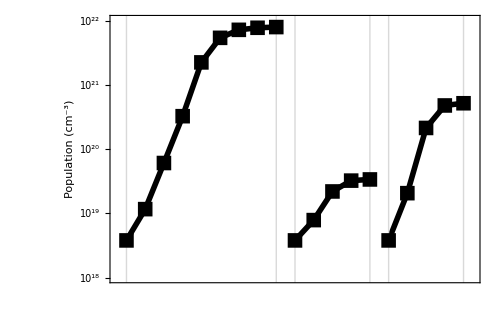

```mathematica
populationc=populationc/(bohr2m^3*10^6);
ListLogPlot[{populationc⟦Range[9],ef0⟧,Table[{i,populationc⟦i,ef0⟧},{i,10,14}],Table[{i,populationc⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]}},PlotMarkers->{{■,15}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,15,25}],None},{None,None}},FrameStyle->Directive[25,Black,Thick],Frame->True,FrameLabel->{None,"Population (cm^-3)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^18,10^22}},GridLines->{{1,9,10,14,15,19},None},GridLinesStyle->Thickness[0.002],ImageSize->500]
populationc=populationc*(bohr2m^3*10^6);
```

### Lifetimes

```mathematica
(* Parameters *)
Δ=0.4;sint=0.5;
Z=1;eps=30;epsinf=25;
vs=4000/(bohr2m/au2sec);ρ=5000/(mass/bohr2m^3);
β=(nr*fratio)/(kB*T*eps);b=(4 mom^2)/β;dopec=1/Z populationc;
fermifunction=1/Gamma[z+1]*NIntegrate[y^z/(1+Exp[y-mu]),{y,0,∞}];
fermiratioc=(fermifunction/.{z->-0.5,mu->Ef/kB/T})/(fermifunction/.{z->0.5,mu->Ef/kB/T});

(* Define Lifetimes *)
taudef=FullSimplify[(π*ρ*vs^2 en^(-1/2))/(Sqrt[2] mdos^(3/2)kB*T*(Δ+mv2)^2)*dos3dpara/dosnew,Assumptions->{en>0,mdos>0}];
taupol=FullSimplify[en^(1/2)/(Sqrt[2]ω*mdos^(1/2))(1/epsinf-1/eps)^-1*mom/(2*en*mdos)^(1/2)*(mdos/mom)*vel(1/(Exp[ω/(kB*T)]-1)(Exp[ω/(kB*T)]*ArcSinh[dosnew1/dosω*HeavisideTheta[en-ω]]+ArcSinh[dosnew2/dosω]))^-1,Assumptions->{en>0,mdos>0}];
tauii=FullSimplify[(Sqrt[2]*mdos^(1/2)*eps^2*en^(3/2))/(π*dope*Z^2)*mom^4/(2*en*mdos)^2*dos3dpara/dosnew*(Log[1+b]-b/(1+b))^-1,Assumptions->{en>0,mdos>0}];

Print["Computing Lifetimes..."]
taupolc=ConstantArray[0,{Nm,Nef,Nk}];taupolcfix=ConstantArray[0,{Nm,Nef,Nk}];
tauiic=ConstantArray[0,{Nm,Nef,Nk}];tauiicfix=ConstantArray[0,{Nm,Nef,Nk}];
taudefc=ConstantArray[0,{Nm,Nef,Nk}];taudefcfix=ConstantArray[0,{Nm,Nef,Nk}];

Do[
(* Polar-Optical Scattering *)
taupolc⟦p,1⟧=taupol/.dosω->(dosatω⟦p⟧+sint*dosatω⟦fix⟧)/.{dosnew1->(dosωk⟦p⟧+sint*dosωkintfix⟦p⟧),dosnew2->(dosk⟦p⟧+sint*doskintfix⟦p⟧),vel->velnorm⟦p⟧,en->Eclist⟦p⟧};
taupolcfix⟦p,1⟧=taupol/.dosω->(dosatω⟦fix⟧+sint*dosatω⟦p⟧)/.{dosnew1->(dosωk⟦fix⟧+sint*dosωkint⟦p⟧),dosnew2->(dosk⟦fix⟧+sint*doskint⟦p⟧),vel->velnorm⟦fix⟧,en->Eclist⟦fix⟧};
Do[taupolc⟦p,ef⟧=taupolc⟦p,1⟧;taupolcfix⟦p,ef⟧=taupolcfix⟦p,1⟧,{ef,2,Nef}];

(* Ionized-Impurity Scattering *)
Do[
tauiic⟦p,ef⟧=tauii/.{nr->populationc⟦p,ef⟧,dope->dopec⟦p,ef⟧,fratio->fermiratioc⟦ef⟧}/.{dosnew->(dosk⟦p⟧+sint*doskintfix⟦p⟧),mom->knorm};
tauiicfix⟦p,ef⟧=tauii/.{nr->populationc⟦p,ef⟧,dope->dopec⟦p,ef⟧,fratio->fermiratioc⟦ef⟧}/.{dosnew->(dosk⟦fix⟧+sint*doskint⟦p⟧),mom->knorm};
,{ef,Nef}];

(* Deformation-Potential Scattering *)
taudefc⟦p,1⟧=taudef/.dosnew->(mv2->mvel2⟦p⟧,dosk⟦p⟧+sint*doskintfix⟦p⟧);
taudefcfix⟦p,1⟧=taudef/.dosnew->(mv2->mvel2⟦fix⟧,dosk⟦fix⟧+sint*doskint⟦p⟧);
Do[taudefc⟦p,ef⟧=taudefc⟦p,1⟧;taudefcfix⟦p,ef⟧=taudefcfix⟦p,1⟧,{ef,2,Nef}];

,{p,Nm}]//AbsoluteTiming

tauc=1/(1/tauiic+1/taudefc+1/taupolc);taucfix=1/(1/tauiicfix+1/taudefcfix+1/taupolcfix);
```

### Calculate Boltzmann Integrals - Conductivity

```mathematica
sigmac=ConstantArray[0,{Nm,Nef}]; sigmapolc=sigmac; sigmadefc=sigmac; sigmaiic=sigmac;
sigmacfix=sigmac;sigmadefcfix=sigmac;sigmapolcfix=sigmac;sigmaiicfix=sigmac;
(*If[Length[Kernels[]]≠$ProcessorCount,
CloseKernels[];LaunchKernels[]
]
SetSharedVariable[sigmadefc,sigmapolc,sigmaiic,sigmac,sigmadefcfix,sigmapolcfix,sigmaiicfix,sigmacfix]
*)
Do[Do[

dfincfix=-dflistc⟦fix⟧/.mu->Ef⟦ef⟧;v2dfcfix=Vc2list⟦fix,1⟧*dfincfix;
dfinc=-dflistc⟦p⟧/.mu->Ef⟦ef⟧;v2dfc=Vc2list⟦p,1⟧*dfinc;

sigmadefc⟦p,ef⟧=Total[taudefc⟦p,ef⟧*v2dfc*wk]/volume;
sigmadefcfix⟦p,ef⟧=Total[taudefcfix⟦p,ef⟧*v2dfcfix*wk]/volume;

sigmapolc⟦p,ef⟧=Total[taupolc⟦p,ef⟧*v2dfc*wk]/volume;
sigmapolcfix⟦p,ef⟧=Total[taupolcfix⟦p,ef⟧*v2dfcfix*wk]/volume;

sigmaiic⟦p,ef⟧=Total[tauiic⟦p,ef⟧*v2dfc*wk]/volume;
sigmaiicfix⟦p,ef⟧=Total[tauiicfix⟦p,ef⟧*v2dfcfix*wk]/volume;

sigmac⟦p,ef⟧=Total[tauc⟦p,ef⟧*v2dfc*wk]/volume;
sigmacfix⟦p,ef⟧=Total[taucfix⟦p,ef⟧*v2dfcfix*wk]/volume;

,{ef,Nef}];
,{p,Nm}]//AbsoluteTiming

sigmac=(sigmac+sigmacfix);
sigmadefc=(sigmadefc+sigmadefcfix);
sigmapolc=(sigmapolc+sigmapolcfix);
sigmaiic=(sigmaiic+sigmaiicfix);
```

{1146.96,Null}

### Calculate Boltzmann Integrals - Thermoelectricity

```mathematica
zetac=ConstantArray[0,{Nm,Nef}];zetadefc=zetac;zetapolc=zetac;zetaiic=zetac;
zetacfix=zetac;zetadefcfix=zetac;zetapolcfix=zetac;zetaiicfix=zetac;
(*If[Length[Kernels[]]≠$ProcessorCount,
CloseKernels[];LaunchKernels[]
]
SetSharedVariable[zetadefc,zetapolc,zetaiic,zetac,zetadefcfix,zetapolcfix,zetaiicfix,zetacfix]
*)
Do[Do[

Ecdifffix=Ef⟦ef⟧-Eclist⟦fix⟧;
dfincfix=-dflistc⟦fix⟧/.mu->Ef⟦ef⟧;
v2dfcfix=Vc2list⟦fix,1⟧*dfincfix;

Ecdiff=Ef⟦ef⟧-Eclist⟦p⟧;
dfinc=-dflistc⟦p⟧/.mu->Ef⟦ef⟧;
v2dfc=Vc2list⟦p,1⟧*dfinc;

zetadefc⟦p,ef⟧=Total[taudefc⟦p,ef⟧*Ecdiff*v2dfc*wk]/volume/T;
zetadefcfix⟦p,ef⟧=Total[taudefcfix⟦p,ef⟧*Ecdifffix*v2dfcfix*wk]/volume/T;

zetapolc⟦p,ef⟧=Total[taupolc⟦p,ef⟧*Ecdiff*v2dfc*wk]/volume/T;
zetapolcfix⟦p,ef⟧=Total[taupolcfix⟦p,ef⟧*Ecdifffix*v2dfcfix*wk]/volume/T;

zetaiic⟦p,ef⟧=Total[tauiic⟦p,ef⟧*Ecdiff*v2dfc*wk]/volume/T;
zetaiicfix⟦p,ef⟧=Total[tauiicfix⟦p,ef⟧*Ecdifffix*v2dfcfix*wk]/volume/T;

zetac⟦p,ef⟧=Total[tauc⟦p,ef⟧*Ecdiff*v2dfc*wk]/volume/T;
zetacfix⟦p,ef⟧=Total[taucfix⟦p,ef⟧*Ecdifffix*v2dfcfix*wk]/volume/T;

,{ef,Nef}];

,{p,Nm}]//AbsoluteTiming

zetac=(zetac+zetacfix);
zetadefc=(zetadefc+zetadefcfix);
zetapolc=(zetapolc+zetapolcfix);
zetaiic=(zetaiic+zetaiicfix);
```

{1119.31,Null}

### Calculate Boltzmann Integrals - Electronic Thermal Conductivity

```mathematica
kappac=ConstantArray[0,{Nm,Nef}];kappadefc=kappac;kappapolc=kappac;kappaiic=kappac;
kappadefcfix=kappac;kappapolcfix=kappac;kappaiicfix=kappac;kappacfix=kappac;

Do[Do[

Ecdiff=Ef⟦ef⟧-Eclist⟦p⟧;
dfinc=-dflistc⟦p⟧/.mu->Ef⟦ef⟧;
v2dfc=Vc2list⟦p,1⟧*dfinc;
Ecdifffix=Ef⟦ef⟧-Eclist⟦fix⟧;
dfincfix=-dflistc⟦fix⟧/.mu->Ef⟦ef⟧;
v2dfcfix=Vc2list⟦fix,1⟧*dfincfix;

kappadefc⟦p,ef⟧=Total[taudefc⟦p,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;
kappapolc⟦p,ef⟧=Total[taupolc⟦p,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;
kappaiic⟦p,ef⟧=Total[tauiic⟦p,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;
kappac⟦p,ef⟧=Total[tauc⟦p,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;

kappadefcfix⟦p,ef⟧=Total[taudefcfix⟦p,ef⟧*Ecdifffix^2*v2dfcfix*wk]/volume/T;
kappapolcfix⟦p,ef⟧=Total[taupolcfix⟦p,ef⟧*Ecdifffix^2*v2dfcfix*wk]/volume/T;
kappaiicfix⟦p,ef⟧=Total[tauiicfix⟦p,ef⟧*Ecdifffix^2*v2dfcfix*wk]/volume/T;
kappacfix⟦p,ef⟧=Total[taucfix⟦p,ef⟧*Ecdifffix^2*v2dfcfix*wk]/volume/T;

,{ef,Nef}];

,{p,Nm}]//AbsoluteTiming

kappac=(kappac+kappacfix)-zetac^2/sigmac*T;
kappadefc=(kappadefc+kappadefcfix)-zetadefc^2/sigmadefc*T;
kappapolc=(kappapolc+kappapolcfix)-zetapolc^2/sigmapolc*T;
kappaiic=(kappaiic+kappaiicfix)-zetaiic^2/sigmaiic*T;
```

{1116.46,Null}

### Find Optimum E_F for PF or zT

```mathematica
optimize="zt";

powerc=zetac^2/sigmac;
powerdefc=zetadefc^2/sigmadefc;
powerpolc=zetapolc^2/sigmapolc;
poweriic=zetaiic^2/sigmaiic;

ztc=powerc*T/(kappac+kappalat);
ztdefc=powerdefc*T/(kappadefc+kappalat);
ztpolc=powerpolc*T/(kappapolc+kappalat);
ztiic=poweriic*T/(kappaiic+kappalat);

index=ConstantArray[0,Nm];
If[optimize=="zt"||optimize=="zT"||optimize=="ZT",
Do[index⟦i⟧=Position[ztc⟦i,All⟧,Max[ztc⟦i,All⟧]]⟦1,1⟧,{i,Nm}]
]
If[optimize=="pf"||optimize=="PF",
Do[index⟦i⟧=Position[powerc⟦i,All⟧,Max[powerc⟦i,All⟧]]⟦1,1⟧,{i,Nm}]
]

mticks=Map[{#⟦1⟧,Rotate[#⟦2⟧,π/4]}&,{{1,0.05},{3,0.5},{5,5},{7,50},{9,500},{10,0.05},{12,5},{14,500},{15,0.05},{17,5},{19,500}}];

fermilevelplot=ListPlot[{Ef⟦index⟦Range[9]⟧⟧*h2ev,Table[{i,Ef⟦index⟦i⟧⟧*h2ev},{i,10,14}],Table[{i,Ef⟦index⟦i⟧⟧*h2ev},{i,15,19}]},PlotStyle->{{Black,Thick}},Frame->True,FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Gray,Dotted,25}},FrameTicks->{{Automatic,None},{mticks,None}},FrameLabel->{None,"E_F for SubscriptBox[StyleBox[\"zT\",FontSlant->\"Italic\"], \"Max\"] (eV)",None,None},Joined->True,PlotRange->{{0.5,Nm+0.5},{-0.2,0.2}},PlotMarkers->{{●,15}},GridLines->{{1,9,10,14,15,19},None},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->600,ImagePadding->100];
carrierplot=ListLogPlot[{Table[{i,populationc⟦i,index⟦i⟧⟧/(bohr2m^3*10^6)},{i,1,9}],Table[{i,populationc⟦i,index⟦i⟧⟧/(bohr2m^3*10^6)},{i,10,14}],Table[{i,populationc⟦i,index⟦i⟧⟧/(bohr2m^3*10^6)},{i,15,19}]},PlotStyle->{{Gray,Dotted,Thick}},Frame->True,FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Gray,Dotted,25}},FrameTicks->{{None,All},{mticks,None}},FrameLabel->{{None,"StyleBox[\"n\",FontSlant->\"Italic\"] for SubscriptBox[StyleBox[\"zT\",FontSlant->\"Italic\"], \"Max\"] (cm^-3)"},{None,None}},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^17,10^22}},PlotMarkers->{{▲,18}},GridLines->{{1,9,10,14,15,19},None},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->600,ImagePadding->100];

Overlay[{fermilevelplot,carrierplot}]
```

### Using Tetrahedron DOS (sint = 0.5)

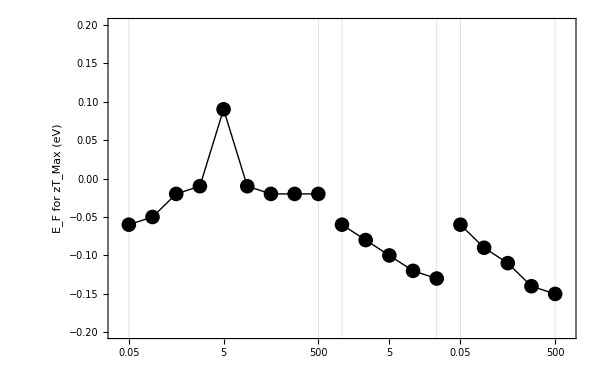
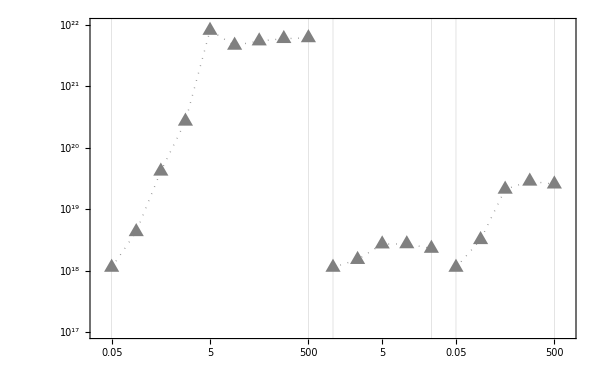

### Using Tetrahedron DOS (sint = 0)

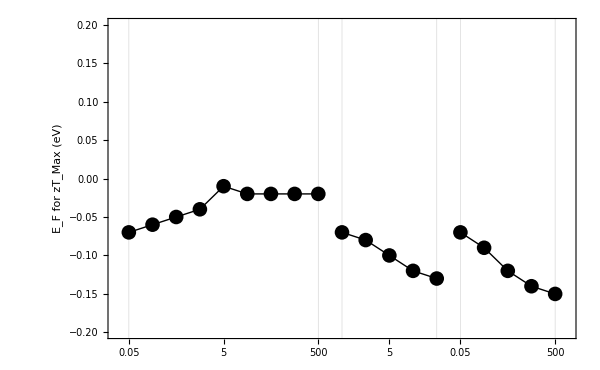
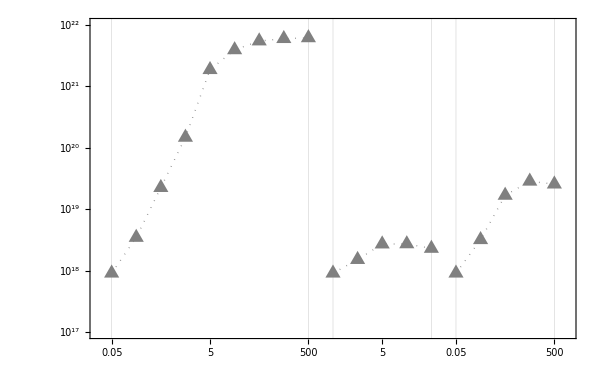

### Conductivity

```mathematica
sigmac=sigmac*au2cond;
sigmadefc=sigmadefc*au2cond;
sigmapolc=sigmapolc*au2cond;
sigmaiic=sigmaiic*au2cond;
ListLogPlot[{Table[{i,sigmac⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmadefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmapolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmaiic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmac⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmadefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmapolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmaiic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmac⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,sigmadefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,sigmapolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,sigmaiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"σ_x (Ω^-1m^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^4,10^8}},GridLines->{{1,9,10,14,15,19},{sigmac⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListLogPlot[{Table[{i,sigmac⟦i,ef0⟧},{i,1,9}],Table[{i,sigmadefc⟦i,ef0⟧},{i,1,9}],Table[{i,sigmapolc⟦i,ef0⟧},{i,1,9}],Table[{i,sigmaiic⟦i,ef0⟧},{i,1,9}],Table[{i,sigmac⟦i,ef0⟧},{i,10,14}],Table[{i,sigmadefc⟦i,ef0⟧},{i,10,14}],Table[{i,sigmapolc⟦i,ef0⟧},{i,10,14}],Table[{i,sigmaiic⟦i,ef0⟧},{i,10,14}],Table[{i,sigmac⟦i,ef0⟧},{i,15,19}],Table[{i,sigmadefc⟦i,ef0⟧},{i,15,19}],Table[{i,sigmapolc⟦i,ef0⟧},{i,15,19}],Table[{i,sigmaiic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"σ_x (Ω^-1m^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^4,10^8}},GridLines->{{1,9,10,14,15,19},{sigmac⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
sigmac=sigmac/au2cond;sigmadefc=sigmadefc/au2cond;sigmapolc=sigmapolc/au2cond;sigmaiic=sigmaiic/au2cond;
```

### Using Tetrahedron DOS (sint = 0.5)

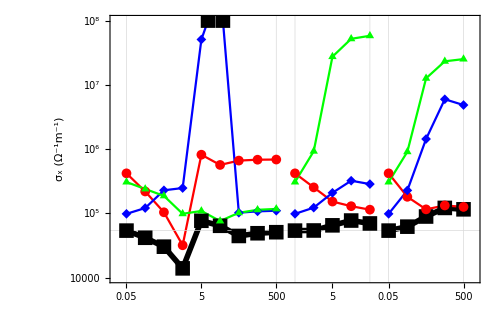

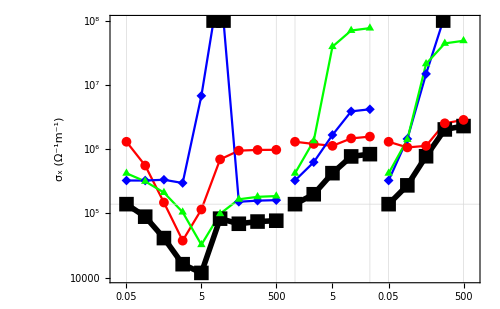

### Using Tetrahedron DOS (sint = 0)

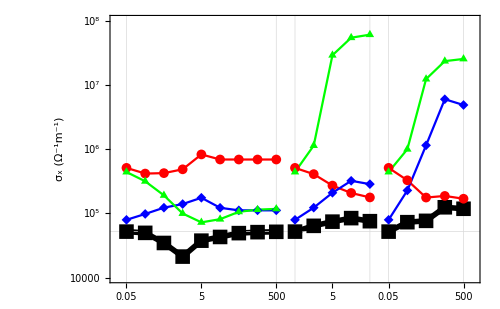

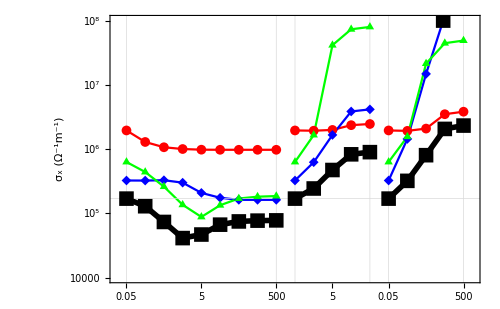

### Mobility

```mathematica
mobdefc=sigmadefc*au2cond/populationc*bohr2m^3/q*10^4;mobpolc=sigmapolc*au2cond/populationc*bohr2m^3/q*10^4;mobiic=sigmaiic*au2cond/populationc*bohr2m^3/q*10^4;
mobc=sigmac*au2cond/populationc*bohr2m^3/q*10^4;

ListLogPlot[{Table[{i,mobc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobdefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobpolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobiic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobdefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobpolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobiic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,mobdefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,mobpolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,mobiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"μ_x (cm^2 V^-1s^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^1,10^5}},GridLines->{{1,9,10,14,15,19},{mobc⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListLogPlot[{Table[{i,mobc⟦i,ef0⟧},{i,1,9}],Table[{i,mobdefc⟦i,ef0⟧},{i,1,9}],Table[{i,mobpolc⟦i,ef0⟧},{i,1,9}],Table[{i,mobiic⟦i,ef0⟧},{i,1,9}],Table[{i,mobc⟦i,ef0⟧},{i,10,14}],Table[{i,mobdefc⟦i,ef0⟧},{i,10,14}],Table[{i,mobpolc⟦i,ef0⟧},{i,10,14}],Table[{i,mobiic⟦i,ef0⟧},{i,10,14}],Table[{i,mobc⟦i,ef0⟧},{i,15,19}],Table[{i,mobdefc⟦i,ef0⟧},{i,15,19}],Table[{i,mobpolc⟦i,ef0⟧},{i,15,19}],Table[{i,mobiic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"μ_x (cm^2 V^-1s^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^1,10^5}},GridLines->{{1,9,10,14,15,19},{mobc⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
```

### Using Tetrahedron DOS (sint = 0.5)

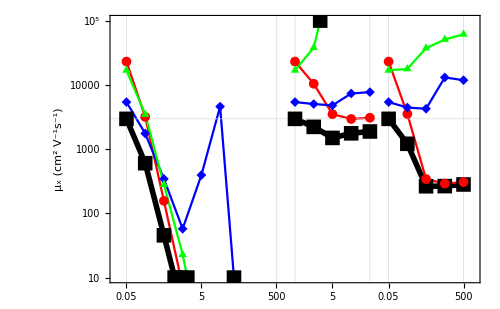

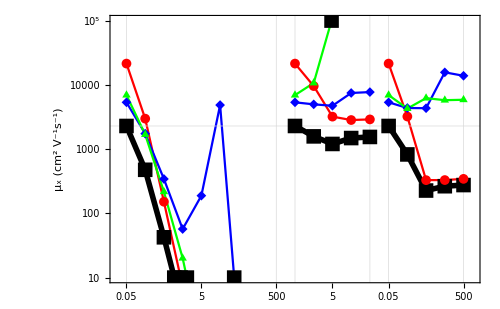

### Using Tetrahedron DOS (sint = 0)

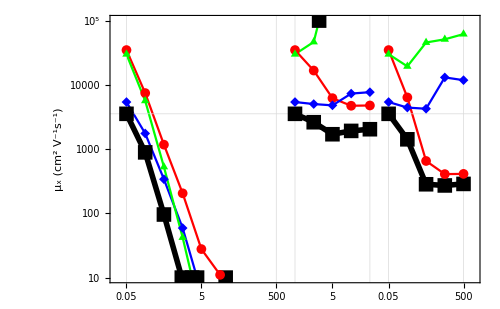

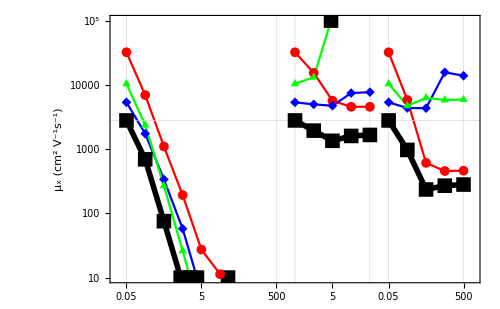

### Using Green's Function DOS

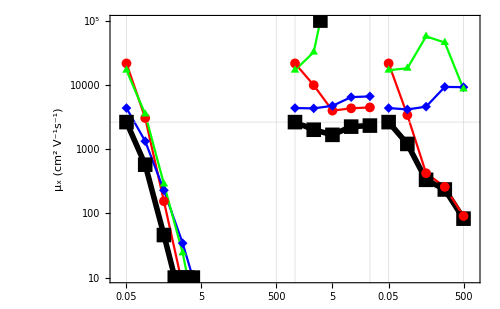

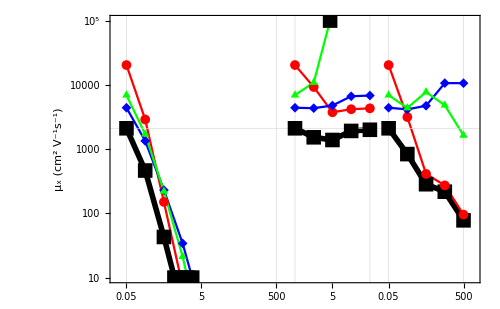

### Thermoelectricity

```mathematica
zetac=zetac*au2cond*h2ev*ev2j/q;zetadefc=zetadefc*au2cond*h2ev*ev2j/q;zetapolc=zetapolc*au2cond*h2ev*ev2j/q;zetaiic=zetaiic*au2cond*h2ev*ev2j/q;
ListLogPlot[{Table[{i,-zetac⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetadefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetapolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetaiic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetac⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetadefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetapolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetaiic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetac⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-zetadefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-zetapolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-zetaiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-ζ_x (A m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^0,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-zetac⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListLogPlot[{Table[{i,-zetac⟦i,ef0⟧},{i,1,9}],Table[{i,-zetadefc⟦i,ef0⟧},{i,1,9}],Table[{i,-zetapolc⟦i,ef0⟧},{i,1,9}],Table[{i,-zetaiic⟦i,ef0⟧},{i,1,9}],Table[{i,-zetac⟦i,ef0⟧},{i,10,14}],Table[{i,-zetadefc⟦i,ef0⟧},{i,10,14}],Table[{i,-zetapolc⟦i,ef0⟧},{i,10,14}],Table[{i,-zetaiic⟦i,ef0⟧},{i,10,14}],Table[{i,-zetac⟦i,ef0⟧},{i,15,19}],Table[{i,-zetadefc⟦i,ef0⟧},{i,15,19}],Table[{i,-zetapolc⟦i,ef0⟧},{i,15,19}],Table[{i,-zetaiic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-ζ_x (A m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^0,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-zetac⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
zetac=zetac/(au2cond*h2ev*ev2j/q);zetadefc=zetadefc/(au2cond*h2ev*ev2j/q);zetapolc=zetapolc/(au2cond*h2ev*ev2j/q);zetaiic=zetaiic/(au2cond*h2ev*ev2j/q);
```

### Using Tetrahedron DOS (sint = 0.5)

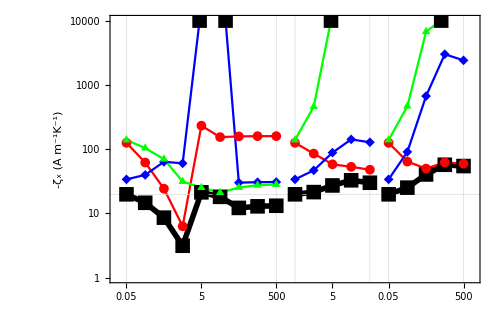

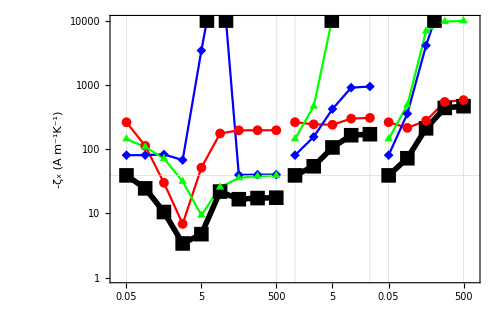

### Using Tetrahedron DOS (sint = 0)

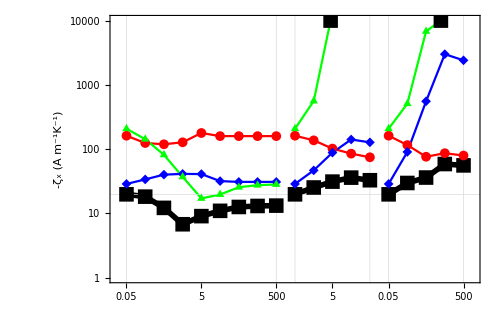

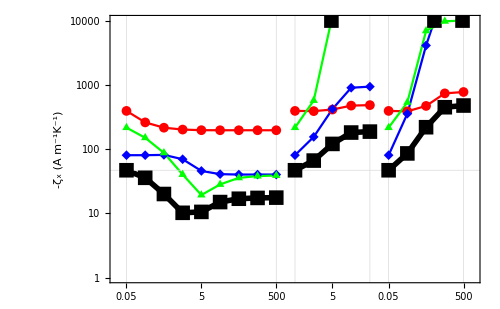

### Using Green's Function DOS

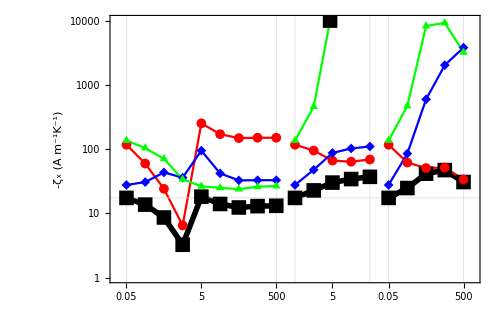

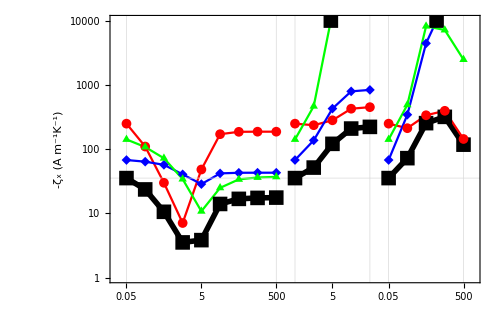

### Power Factor

```mathematica
dir =1;
powerc=powerc*au2cond*(h2ev*ev2j/q)^2*10^3;powerdefc=powerdefc*au2cond*(h2ev*ev2j/q)^2*10^3;powerpolc=powerpolc*au2cond*(h2ev*ev2j/q)^2*10^3;poweriic=poweriic*au2cond*(h2ev*ev2j/q)^2*10^3;
ListLogPlot[{Table[{i,powerc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,powerdefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,powerpolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,poweriic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,powerc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,powerdefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,powerpolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,poweriic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,powerc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,powerdefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,powerpolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,poweriic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"PF_x (mW m^-1K^-2)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-1,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{Max[powerc⟦1,index⟦1⟧⟧]}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListLogPlot[{powerc⟦Range[9],ef0⟧,powerdefc⟦Range[9],ef0⟧,powerpolc⟦Range[9],ef0⟧,poweriic⟦Range[9],ef0⟧,Table[{i,powerc⟦i,ef0⟧},{i,10,14}],Table[{i,powerdefc⟦i,ef0⟧},{i,10,14}],Table[{i,powerpolc⟦i,ef0⟧},{i,10,14}],Table[{i,poweriic⟦i,ef0⟧},{i,10,14}],Table[{i,powerc⟦i,ef0⟧},{i,15,19}],Table[{i,powerdefc⟦i,ef0⟧},{i,15,19}],Table[{i,powerpolc⟦i,ef0⟧},{i,15,19}],Table[{i,poweriic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"PF_x (mW m^-1K^-2)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-1,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{powerc⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
powerc=powerc/(au2cond*(h2ev*ev2j/q)^2*10^3);powerdefc=powerdefc/(au2cond*(h2ev*ev2j/q)^2*10^3);
powerpolc=powerpolc/(au2cond*(h2ev*ev2j/q)^2*10^3);poweriic=poweriic/(au2cond*(h2ev*ev2j/q)^2*10^3);
```

### Using Tetrahedron DOS (sint = 0.5)

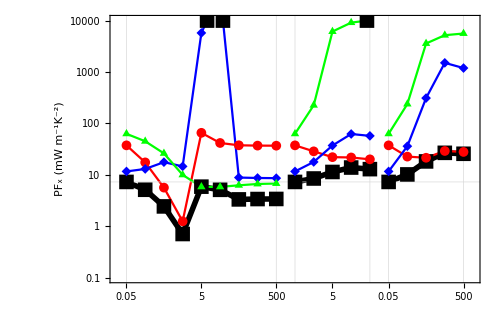

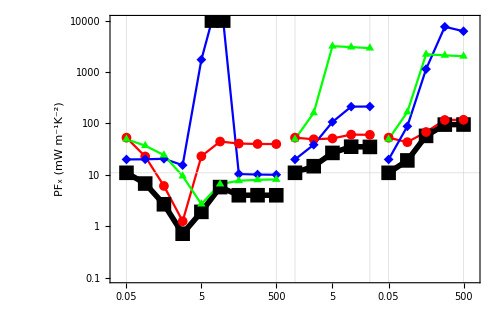

### Using Tetrahedron DOS (sint = 0)

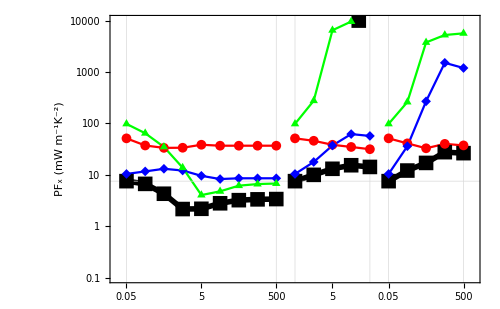

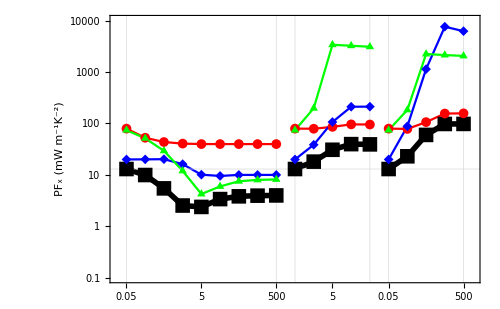

### Using Green's Function DOS

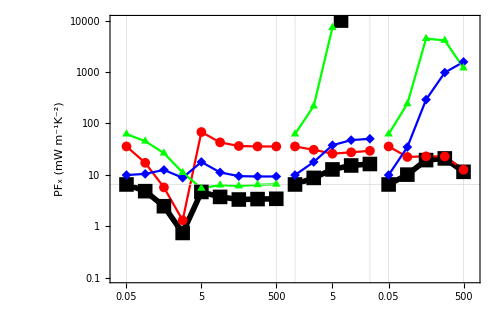

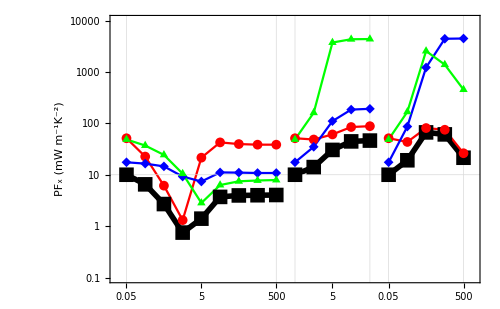

### Seebeck Coefficient

```mathematica
alphac=zetac/sigmac;
alphadefc=zetadefc/sigmadefc;
alphapolc=zetapolc/sigmapolc;
alphaiic=zetaiic/sigmaiic;

alphac=alphac*h2ev*ev2j/q*10^6;alphadefc=alphadefc*h2ev*ev2j/q*10^6;alphapolc=alphapolc*h2ev*ev2j/q*10^6;alphaiic=alphaiic*h2ev*ev2j/q*10^6;
ListPlot[{Table[{i,-alphac⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphadefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphapolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphaiic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphac⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphadefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphapolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphaiic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphac⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-alphadefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-alphapolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-alphaiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-α_x (μV K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,600}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-alphac⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListPlot[{Table[{i,-alphac⟦i,ef0⟧},{i,1,9}],Table[{i,-alphadefc⟦i,ef0⟧},{i,1,9}],Table[{i,-alphapolc⟦i,ef0⟧},{i,1,9}],Table[{i,-alphaiic⟦i,ef0⟧},{i,1,9}],Table[{i,-alphac⟦i,ef0⟧},{i,10,14}],Table[{i,-alphadefc⟦i,ef0⟧},{i,10,14}],Table[{i,-alphapolc⟦i,ef0⟧},{i,10,14}],Table[{i,-alphaiic⟦i,ef0⟧},{i,10,14}],Table[{i,-alphac⟦i,ef0⟧},{i,15,19}],Table[{i,-alphadefc⟦i,ef0⟧},{i,15,19}],Table[{i,-alphapolc⟦i,ef0⟧},{i,15,19}],Table[{i,-alphaiic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-α_x (μV K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,500}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-alphac⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
alphac=alphac/(h2ev*ev2j/q*10^6);alphadefc=alphadefc/(h2ev*ev2j/q*10^6);alphapolc=alphapolc/(h2ev*ev2j/q*10^6);alphaiic=alphaiic/(h2ev*ev2j/q*10^6);
```

### Using Tetrahedron DOS (sint = 0.5)

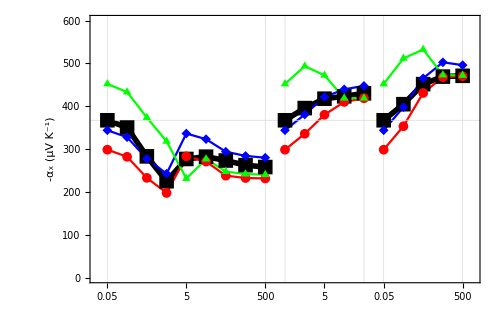

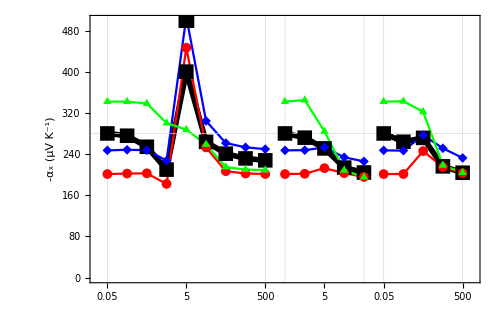

### Using Tetrahedron DOS (sint = 0)

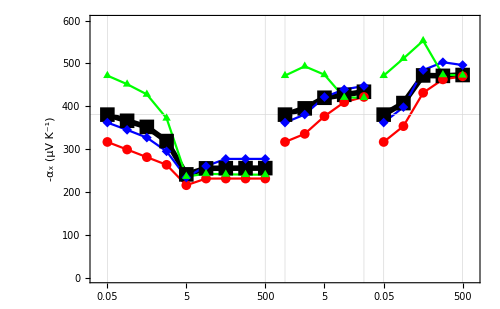

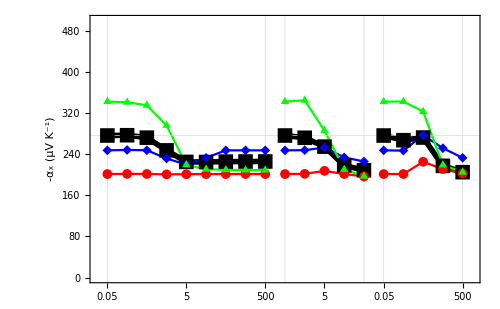

### Using Green's Function DOS

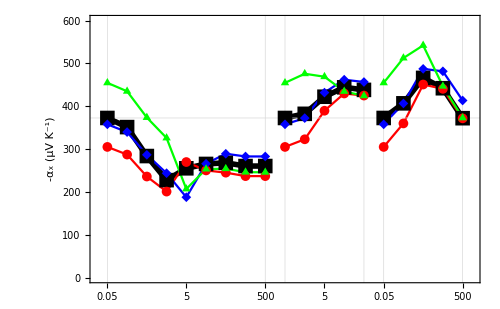

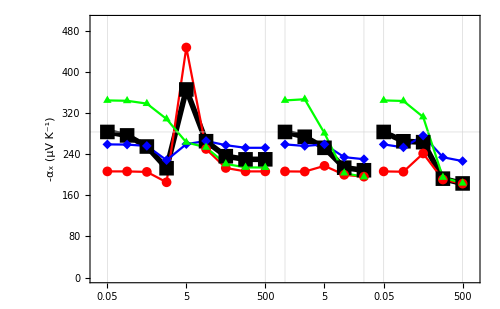

### Electronic Thermal Conductivity

```mathematica
kappac=kappac*h2ev*ev2j/bohr2m/au2sec;kappadefc=kappadefc*h2ev*ev2j/bohr2m/au2sec;kappapolc=kappapolc*h2ev*ev2j/bohr2m/au2sec;kappaiic=kappaiic*h2ev*ev2j/bohr2m/au2sec;
ListLogPlot[{Table[{i,kappac⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappadefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappapolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappaiic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappac⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappadefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappapolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappaiic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappac⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,kappadefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,kappapolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,kappaiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"κ_(e,  x) (W m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-2,10^3}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{kappac⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListLogPlot[{Table[{i,kappac⟦i,ef0⟧},{i,1,9}],Table[{i,kappadefc⟦i,ef0⟧},{i,1,9}],Table[{i,kappapolc⟦i,ef0⟧},{i,1,9}],Table[{i,kappaiic⟦i,ef0⟧},{i,1,9}],Table[{i,kappac⟦i,ef0⟧},{i,10,14}],Table[{i,kappadefc⟦i,ef0⟧},{i,10,14}],Table[{i,kappapolc⟦i,ef0⟧},{i,10,14}],Table[{i,kappaiic⟦i,ef0⟧},{i,10,14}],Table[{i,kappac⟦i,ef0⟧},{i,15,19}],Table[{i,kappadefc⟦i,ef0⟧},{i,15,19}],Table[{i,kappapolc⟦i,ef0⟧},{i,15,19}],Table[{i,kappaiic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"κ_(e,  x) (W m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-2,10^3}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{kappac⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
kappac=kappac/(h2ev*ev2j/bohr2m/au2sec);kappadefc=kappadefc/(h2ev*ev2j/bohr2m/au2sec);kappapolc=kappapolc/(h2ev*ev2j/bohr2m/au2sec);kappaiic=kappaiic/(h2ev*ev2j/bohr2m/au2sec);
```

### Using Tetrahedron DOS (sint = 0.5)

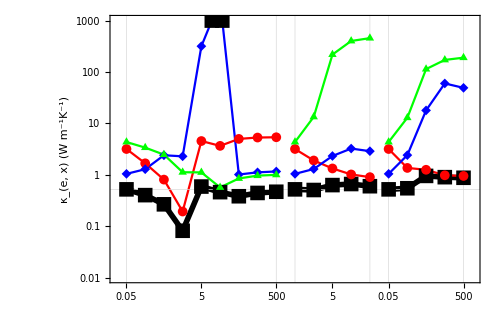

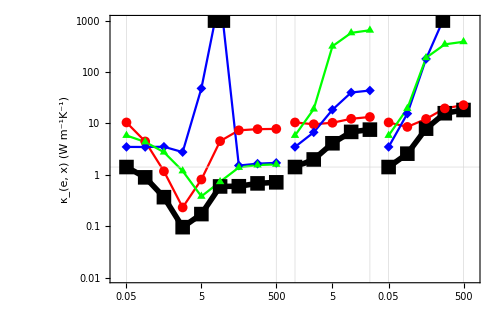

### Using Tetrahedron DOS (sint = 0)

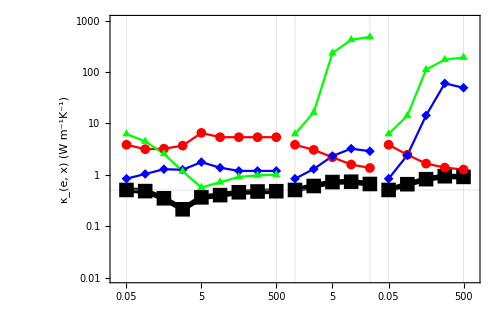

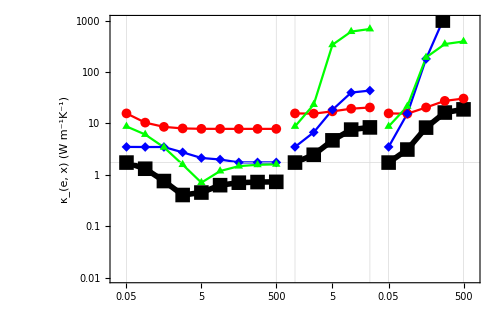

### Using Green's Function DOS

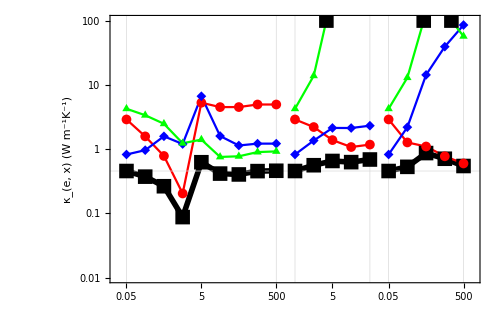

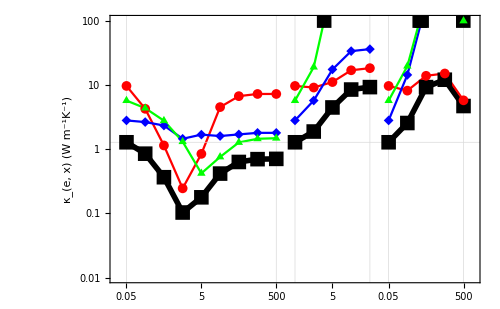

### Lorenz Number

```mathematica
lorenzc=kappac/sigmac/T;
lorenzdefc=kappadefc/sigmadefc/T;
lorenzpolc=kappapolc/sigmapolc/T;
lorenziic=kappaiic/sigmaiic/T;

lorenzc=lorenzc*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;lorenzdefc=lorenzdefc*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
lorenzpolc=lorenzpolc*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
lorenziic=lorenziic*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
ListPlot[{Table[{i,lorenzc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenzdefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenzpolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenziic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenzc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenzdefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenzpolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenziic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenzc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,lorenzdefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,lorenzpolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,lorenziic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},FrameLabel->{None,"L_x (10^-8WΩK^-2)"},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{{2.44,Dotted},{lorenzc⟦1,index⟦1⟧⟧,Dashed}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListPlot[{Table[{i,lorenzc⟦i,ef0⟧},{i,1,9}],Table[{i,lorenzdefc⟦i,ef0⟧},{i,1,9}],Table[{i,lorenzpolc⟦i,ef0⟧},{i,1,9}],Table[{i,lorenziic⟦i,ef0⟧},{i,1,9}],Table[{i,lorenzc⟦i,ef0⟧},{i,10,14}],Table[{i,lorenzdefc⟦i,ef0⟧},{i,10,14}],Table[{i,lorenzpolc⟦i,ef0⟧},{i,10,14}],Table[{i,lorenziic⟦i,ef0⟧},{i,10,14}],Table[{i,lorenzc⟦i,ef0⟧},{i,15,19}],Table[{i,lorenzdefc⟦i,ef0⟧},{i,15,19}],Table[{i,lorenzpolc⟦i,ef0⟧},{i,15,19}],Table[{i,lorenziic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},FrameLabel->{None,"L_x (10^-8WΩK^-2)"},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{{2.44,Dotted},{lorenzc⟦1,ef0⟧,Dashed}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black}},ImageSize->500]
lorenzc=lorenzc/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);lorenzdefc=lorenzdefc/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
lorenzpolc=lorenzpolc/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
lorenziic=lorenziic/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
```

### Using Tetrahedron DOS (sint = 0.5)

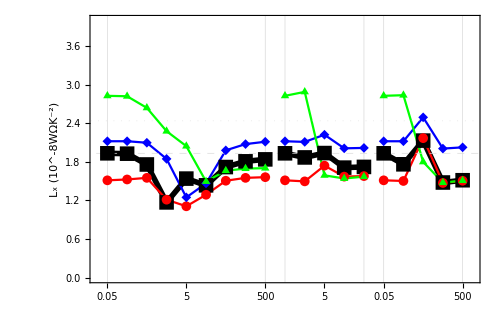

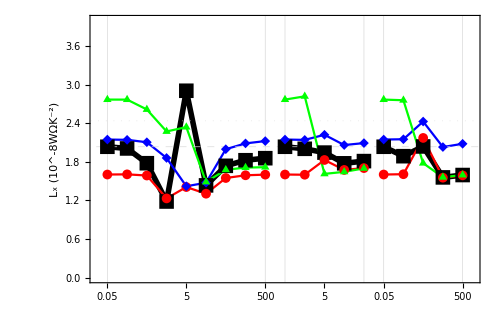

### Using Tetrahedron DOS (sint = 0)

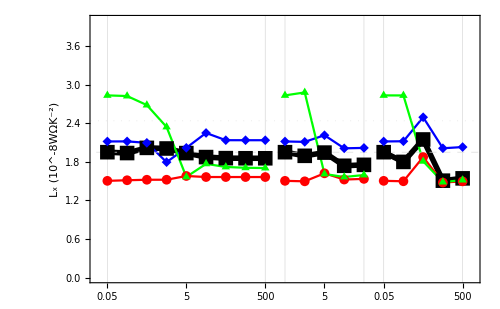

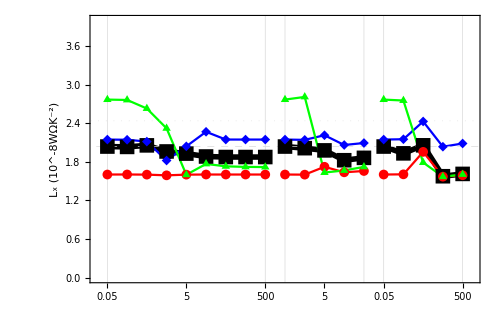

### ZT

```mathematica
ListPlot[{Table[{i,ztc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztdefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztpolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztiic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztdefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztpolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztiic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztdefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztpolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"zT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,12}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztc⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListPlot[{Table[{i,ztc⟦i,ef0⟧},{i,1,9}],Table[{i,ztdefc⟦i,ef0⟧},{i,1,9}],Table[{i,ztpolc⟦i,ef0⟧},{i,1,9}],Table[{i,ztiic⟦i,ef0⟧},{i,1,9}],Table[{i,ztc⟦i,ef0⟧},{i,10,14}],Table[{i,ztdefc⟦i,ef0⟧},{i,10,14}],Table[{i,ztpolc⟦i,ef0⟧},{i,10,14}],Table[{i,ztiic⟦i,ef0⟧},{i,10,14}],Table[{i,ztc⟦i,ef0⟧},{i,15,19}],Table[{i,ztdefc⟦i,ef0⟧},{i,15,19}],Table[{i,ztpolc⟦i,ef0⟧},{i,15,19}],Table[{i,ztiic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"zT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,20}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztc⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
```

### Using Tetrahedron DOS (sint = 0.5)

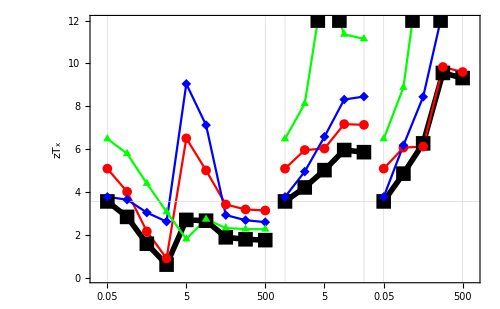

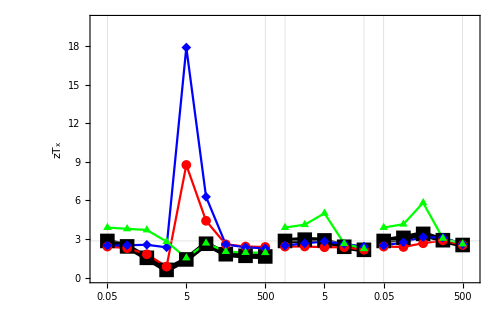

### Using Tetrahedron DOS (sint = 0)

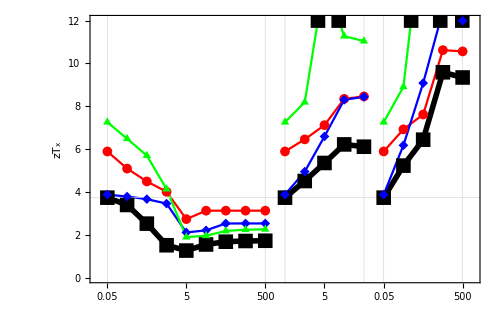

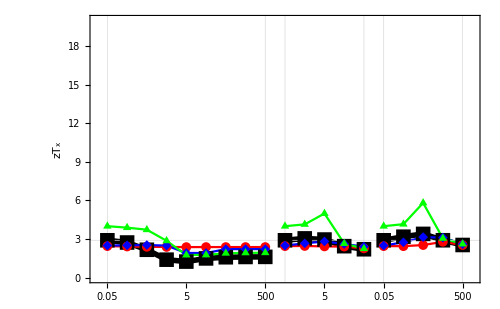

### Electronic-part zT

```mathematica
ztec=powerc*T/(kappac);
ztedefc=powerdefc*T/(kappadefc);
ztepolc=powerpolc*T/(kappapolc);
zteiic=poweriic*T/(kappaiic);

ListPlot[{Table[{i,ztec⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztedefc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztepolc⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,zteiic⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztec⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztedefc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztepolc⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,zteiic⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztec⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztedefc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztepolc⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,zteiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thick},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"z_eT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,20}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztec⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
ef0=Position[Ef,0.]⟦1,1⟧;
ListPlot[{Table[{i,ztec⟦i,ef0⟧},{i,1,9}],Table[{i,ztedefc⟦i,ef0⟧},{i,1,9}],Table[{i,ztepolc⟦i,ef0⟧},{i,1,9}],Table[{i,zteiic⟦i,ef0⟧},{i,1,9}],Table[{i,ztec⟦i,ef0⟧},{i,10,14}],Table[{i,ztedefc⟦i,ef0⟧},{i,10,14}],Table[{i,ztepolc⟦i,ef0⟧},{i,10,14}],Table[{i,zteiic⟦i,ef0⟧},{i,10,14}],Table[{i,ztec⟦i,ef0⟧},{i,15,19}],Table[{i,ztedefc⟦i,ef0⟧},{i,15,19}],Table[{i,ztepolc⟦i,ef0⟧},{i,15,19}],Table[{i,zteiic⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thick},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"z_eT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,20}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztec⟦1,ef0⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
```

### Using Tetrahedron DOS (sint = 0.5)

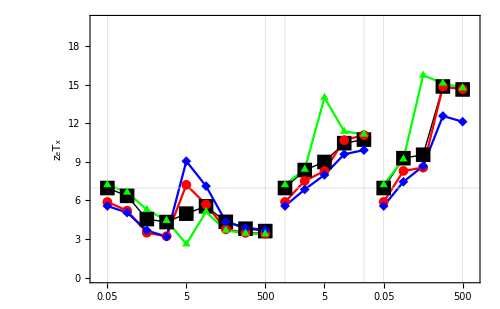

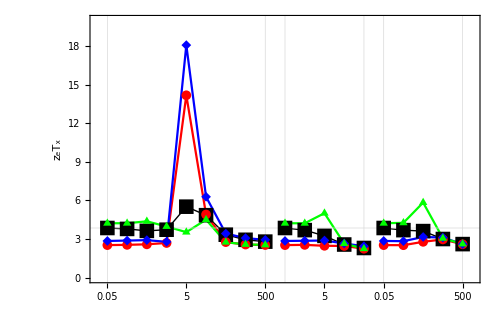

### Using Tetrahedron DOS (sint = 0)